#### Function list dump

pipe
pipeList
branch
branchSeq
deCurry
nativeSize
checkerboard
gammaDecode
gammaEncode
imgGammaDecode
imgGammaEncode
levelIndentFunc
horizontalTreeForm
GraphEdgeSleek
toRegularArray
inputHistoryViewer
StringSplitNested
colorFromHex
colorToHex
DatasetGrid
multiDimGrid
randomIntegerPartitions

```mathematica
Needs["SilviaCollection`"]
```

```mathematica
x//pipe[f,h,g]
```

g[h[f[x]]]

```mathematica
x//pipeList[f,h,g]
```

{x,f[x],h[f[x]],g[h[f[x]]]}

```mathematica
x//branch[f,h,g]
```

{f[x],h[x],g[x]}

```mathematica
x//branchSeq[f,h,g]//F
```

F[f[x],h[x],g[x]]

```mathematica
f[1,2,3,4]//deCurry
```

f[1][2][3][4]

Gamma correction is important:

```mathematica
{
ConstantImage[RGBColor[0.1725, 0.5767499999999999, 0.75],{101,101}]
,ConstantImage[RGBColor[0.88, 0.2024, 0.2024],{101,101}]
,Image[GaussianMatrix[{50,30}]//Rescale]
}//pipeList[
branch[First,pipe[Rest,Apply@SetAlphaChannel]]
,branch[Identity,Map@pipe[branchSeq[pipe[RemoveAlphaChannel,imgGammaDecode],AlphaChannel],SetAlphaChannel]]
,ImageCompose@@@#&,Map@RemoveAlphaChannel
,branch[First,pipe[Last,imgGammaEncode]]
]//pipe[
Rest,Append[{"↑ wrong blend","↑ correct blend"}]
,Grid[#,Frame->All,ItemSize->Full]&
]
```

-Graphics- | -Graphics-
{-Graphics-,-Graphics-} | {-Graphics-,-Graphics-}
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
↑ wrong blend | ↑ correct blend

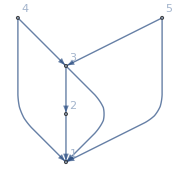

```mathematica
mygraph=Graph[{1,2,3,4,5},{2->1,3->1,3->2,4->1,4->3,5->1,5->3},VertexLabels->"Name",ImageSize->Small]
```

```mathematica
mygraph//GraphEdgeSleek
```

-Graphics-

```mathematica
RandomInteger[{0,9},4]//multiDimGrid
```

1 | 2 | 3 | 4
3 | 9 | 5 | 6

```mathematica
RandomInteger[{0,9},{2,3}]//multiDimGrid
```

| 1 | 2 | 3
1 | 6 | 2 | 2
2 | 0 | 6 | 6

```mathematica
RandomInteger[{0,9},{2,3,4}]//multiDimGrid
```

1 |  |  |  |  | 2 |  |  |  | 
 | 1 | 2 | 3 | 4 |  | 1 | 2 | 3 | 4
1 | 7 | 3 | 9 | 0 | 1 | 9 | 7 | 2 | 5
2 | 6 | 2 | 8 | 2 | 2 | 5 | 4 | 5 | 3
3 | 1 | 3 | 6 | 9 | 3 | 9 | 3 | 6 | 8

```mathematica
RandomInteger[{0,9},{2,3,4,2,1,2,3}]//multiDimGrid
```

1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 2 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |  |  |  |  | 2 |  |  |  |  | 3 |  |  |  |  | 4 |  |  |  |  |  | 1 |  |  |  |  | 2 |  |  |  |  | 3 |  |  |  |  | 4 |  |  |  | 
1 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  | 1 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  | 
 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 |  | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3
 |  | 1 | 6 | 6 | 7 |  | 1 | 6 | 6 | 7 |  | 1 | 0 | 8 | 1 |  | 1 | 1 | 7 | 2 |  |  | 1 | 9 | 4 | 4 |  | 1 | 4 | 7 | 8 |  | 1 | 3 | 0 | 6 |  | 1 | 0 | 2 | 8
 |  | 2 | 8 | 9 | 2 |  | 2 | 4 | 1 | 5 |  | 2 | 0 | 6 | 7 |  | 2 | 2 | 1 | 5 |  |  | 2 | 9 | 5 | 6 |  | 2 | 5 | 9 | 1 |  | 2 | 0 | 3 | 2 |  | 2 | 2 | 1 | 6
 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 |  | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3
 |  | 1 | 8 | 3 | 0 |  | 1 | 6 | 9 | 9 |  | 1 | 5 | 5 | 8 |  | 1 | 4 | 5 | 4 |  |  | 1 | 4 | 5 | 1 |  | 1 | 2 | 4 | 4 |  | 1 | 6 | 1 | 6 |  | 1 | 0 | 6 | 0
 |  | 2 | 8 | 8 | 3 |  | 2 | 6 | 0 | 1 |  | 2 | 3 | 9 | 9 |  | 2 | 5 | 1 | 0 |  |  | 2 | 0 | 6 | 1 |  | 2 | 8 | 4 | 8 |  | 2 | 7 | 4 | 2 |  | 2 | 5 | 8 | 6
2 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  | 2 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  | 
 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 |  | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3
 |  | 1 | 7 | 2 | 9 |  | 1 | 0 | 0 | 3 |  | 1 | 2 | 7 | 5 |  | 1 | 4 | 1 | 8 |  |  | 1 | 3 | 9 | 1 |  | 1 | 1 | 8 | 5 |  | 1 | 2 | 1 | 0 |  | 1 | 9 | 2 | 9
 |  | 2 | 5 | 4 | 2 |  | 2 | 6 | 3 | 6 |  | 2 | 8 | 7 | 8 |  | 2 | 8 | 6 | 4 |  |  | 2 | 9 | 1 | 7 |  | 2 | 4 | 5 | 9 |  | 2 | 5 | 5 | 4 |  | 2 | 0 | 2 | 7
 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 |  | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3
 |  | 1 | 0 | 7 | 4 |  | 1 | 4 | 0 | 0 |  | 1 | 4 | 1 | 0 |  | 1 | 2 | 7 | 5 |  |  | 1 | 4 | 9 | 4 |  | 1 | 5 | 7 | 2 |  | 1 | 8 | 1 | 0 |  | 1 | 0 | 1 | 9
 |  | 2 | 7 | 6 | 5 |  | 2 | 9 | 9 | 4 |  | 2 | 9 | 6 | 2 |  | 2 | 4 | 7 | 2 |  |  | 2 | 3 | 4 | 5 |  | 2 | 8 | 3 | 9 |  | 2 | 0 | 9 | 3 |  | 2 | 6 | 8 | 1
3 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  | 3 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  | 
 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 |  | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3
 |  | 1 | 1 | 3 | 1 |  | 1 | 6 | 2 | 0 |  | 1 | 5 | 9 | 3 |  | 1 | 5 | 0 | 9 |  |  | 1 | 6 | 5 | 9 |  | 1 | 2 | 4 | 5 |  | 1 | 1 | 2 | 5 |  | 1 | 5 | 9 | 0
 |  | 2 | 2 | 3 | 4 |  | 2 | 2 | 3 | 1 |  | 2 | 8 | 4 | 3 |  | 2 | 1 | 0 | 5 |  |  | 2 | 3 | 7 | 1 |  | 2 | 7 | 2 | 5 |  | 2 | 2 | 1 | 2 |  | 2 | 9 | 9 | 3
 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 |  | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3
 |  | 1 | 4 | 7 | 7 |  | 1 | 9 | 9 | 1 |  | 1 | 5 | 8 | 2 |  | 1 | 9 | 7 | 0 |  |  | 1 | 1 | 0 | 1 |  | 1 | 6 | 0 | 0 |  | 1 | 3 | 9 | 9 |  | 1 | 2 | 7 | 7
 |  | 2 | 9 | 5 | 9 |  | 2 | 9 | 0 | 8 |  | 2 | 4 | 1 | 0 |  | 2 | 5 | 3 | 1 |  |  | 2 | 6 | 0 | 3 |  | 2 | 5 | 5 | 8 |  | 2 | 3 | 6 | 6 |  | 2 | 6 | 0 | 5

```mathematica
randomIntegerPartitions[10,5,3] // pipe[Transpose,Join[#,Thread[{" ∑ ⟹ ",Total@#}]ᵀ]&,Transpose,Grid]
```

2 | 1 | 2 | 4 | 1 |  ∑ ⟹  | 10
3 | 3 | 1 | 2 | 1 |  ∑ ⟹  | 10
2 | 2 | 2 | 2 | 2 |  ∑ ⟹  | 10